```mathematica
R=10;
n=21;
h=R/(n-1);
```

```mathematica
symm[i_]=If[i>=1,i,2-i];
```

```mathematica
(grad2=1/h Table[
(If[j==symm[i-1],-1,0]+
If[j==symm[i+1],+1,0])/2,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(grad4=1/h Table[
(If[j==symm[i-2],+1,0]+
If[j==symm[i-1],-8,0]+
If[j==symm[i+1],+8,0]+
If[j==symm[i+2],-1,0])/12,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(grad6=1/h Table[
(If[j==symm[i-3],-1,0]+
If[j==symm[i-2],+9,0]+
If[j==symm[i-1],-180/4,0]+
If[j==symm[i+1],180/4,0]+
If[j==symm[i+2],-9,0]+
If[j==symm[i+3],+1,0])/60,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(grad8=1/h Table[
(     If[j==symm[i-4],+1,0]+
If[j==symm[i-3],-(280*4)/105,0]+
If[j==symm[i-2],+280/5,0]+
If[j==symm[i-1],-280*4/5,0]+
If[j==symm[i+1],+280*4/5,0]+
If[j==symm[i+2],-280/5,0]+
If[j==symm[i+3],+(280*4)/105,0]+
If[j==symm[i+4],-1,0])/280,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(W=h DiagonalMatrix[Table[
If[i==1,1/2,1],
{i,n}]])//MatrixForm;
```

```mathematica
(QS= (DiagonalMatrix[Table[q[i],
{i,n}]]+
SparseArray[{{1,2}->q[1,2],{2,1}->q[1,2],{2,3}->q[2,3],{3,2}->q[2,3]},{n,n}]))//MatrixForm
```

(q[1] | q[1,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | q[2,3] | q[3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | q[4] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | q[6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | q[7] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[12] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[13] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[14] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[15] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[16] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[17] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[18] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[19] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[20] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[21])

```mathematica
(QV=DiagonalMatrix[Table[q[i],{i,n}]])//MatrixForm
```

(q[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | q[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | q[3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | q[4] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | q[6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | q[7] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[12] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[13] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[14] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[15] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[16] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[17] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[18] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[19] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[20] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[21])

```mathematica
(B=DiagonalMatrix[Table[0,{i,n}]])//MatrixForm;
```

```mathematica
(div2=Inverse[W].Transpose[B-W.grad2])//MatrixForm;
(div4=Inverse[W].Transpose[B-W.grad4])//MatrixForm;
(div6=Inverse[W].Transpose[B-W.grad6])//MatrixForm;
(div8=Inverse[W].Transpose[B-W.grad8])//MatrixForm;
SDIV4= Inverse[QS].div4.QV//MatrixForm;
```

```mathematica
(c=Table[1,{i,n}])//MatrixForm;
```

```mathematica
(r=h Table[i-1,{i,n}])//MatrixForm
```

(0
1/2
1
3/2
2
5/2
3
7/2
4
9/2
5
11/2
6
13/2
7
15/2
8
17/2
9
19/2
10)

```mathematica
(div6.r^5-5r^4)[[;;]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1361367/320,31603277/960,-3595955/24}

```mathematica
div2.r
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-19/2}

```mathematica
grad4.c
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/6,-7/6}

```mathematica
(grad8.r^6-6r^5)[[;;-4]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12252303/1280}

```mathematica
grad6.r^4-4r^3
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-64827/160,1516073/480,-3461591/240}

```mathematica
div8.r^3-3 r^2
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1323/160,-11017/140,1251613/3360,-4270/3}

```mathematica
(cond2=div2.QV.r-3QV.c)//MatrixForm
```

(-3 q[1]+q[2]
-3 q[2]+q[3]
-q[2]/2-3 q[3]+(3 q[4])/2
-q[3]-3 q[4]+2 q[5]
-(3 q[4])/2-3 q[5]+(5 q[6])/2
-2 q[5]-3 q[6]+3 q[7]
-(5 q[6])/2-3 q[7]+(7 q[8])/2
-3 q[7]-3 q[8]+4 q[9]
-(7 q[8])/2-3 q[9]+(9 q[10])/2
-4 q[9]-3 q[10]+5 q[11]
-(9 q[10])/2-3 q[11]+(11 q[12])/2
-5 q[11]-3 q[12]+6 q[13]
-(11 q[12])/2-3 q[13]+(13 q[14])/2
-6 q[13]-3 q[14]+7 q[15]
-(13 q[14])/2-3 q[15]+(15 q[16])/2
-7 q[15]-3 q[16]+8 q[17]
-(15 q[16])/2-3 q[17]+(17 q[18])/2
-8 q[17]-3 q[18]+9 q[19]
-(17 q[18])/2-3 q[19]+(19 q[20])/2
-9 q[19]-3 q[20]+10 q[21]
-(19 q[20])/2-3 q[21])

```mathematica
cond22=Join[cond2[[1;;-2]],{q[n]-r[[n]]^2}]
```

{-3 q[1]+q[2],-3 q[2]+q[3],-q[2]/2-3 q[3]+(3 q[4])/2,-q[3]-3 q[4]+2 q[5],-(3 q[4])/2-3 q[5]+(5 q[6])/2,-2 q[5]-3 q[6]+3 q[7],-(5 q[6])/2-3 q[7]+(7 q[8])/2,-3 q[7]-3 q[8]+4 q[9],-(7 q[8])/2-3 q[9]+(9 q[10])/2,-4 q[9]-3 q[10]+5 q[11],-(9 q[10])/2-3 q[11]+(11 q[12])/2,-5 q[11]-3 q[12]+6 q[13],-(11 q[12])/2-3 q[13]+(13 q[14])/2,-6 q[13]-3 q[14]+7 q[15],-(13 q[14])/2-3 q[15]+(15 q[16])/2,-7 q[15]-3 q[16]+8 q[17],-(15 q[16])/2-3 q[17]+(17 q[18])/2,-8 q[17]-3 q[18]+9 q[19],-(17 q[18])/2-3 q[19]+(19 q[20])/2,-9 q[19]-3 q[20]+10 q[21],-100+q[21]}

```mathematica
cond22[[5]]-Sum[D[cond22[[5]],q[i]]*q[i],{i,n}]
```

0

```mathematica
(sol2=Solve[cond22==0,Table[q[i],{i,n}]][[1]])//MatrixForm
```

(q[1]→100/801
q[2]→100/267
q[3]→100/89
q[4]→1900/801
q[5]→1100/267
q[6]→1700/267
q[7]→7300/801
q[8]→1100/89
q[9]→4300/267
q[10]→16300/801
q[11]→6700/267
q[12]→2700/89
q[13]→28900/801
q[14]→11300/267
q[15]→13100/267
q[16]→45100/801
q[17]→5700/89
q[18]→19300/267
q[19]→64900/801
q[20]→24100/267
q[21]→100)

```mathematica
QQV2=QV/.sol2;
DDIV2=Inverse[QQV2].div2.QQV2;
DDIV2.r//FullSimplify
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,-4579/534}

```mathematica
(cond4a = div4.QV.r-3QS.c)//MatrixForm;
(cond4b=div4.QV.r^3-5QS.r^2)//MatrixForm;
(*(cond4b2=div4.QV.r^3-5QS.r^2 )//MatrixForm;*)
```

```mathematica
(condw4=Join[cond4a[[;;-3,All]],cond4b[[;;2,All]],{q[n-1]-(r[[n-1]]^2+0/2 h^2),q[n]-(r[[n]]^2+0/2 h^2)}])//MatrixForm;
(vars = DeleteDuplicates[SparseArray[QS]["NonzeroValues"]])//MatrixForm;
Length[vars]
Length[condw4]
(*(solq4=Reduce[condw4==0,vars,Reals,Backsubstitution->True][[1]]//ToRules)//N//MatrixForm*)
(solq4=Solve[condw4==0,vars][[1]])//MatrixForm
```

23

23

(q[1]→2621114103693576605431157547/10391487621754639992384548431
q[1,2]→-1478365760311215810641252051/10391487621754639992384548431
q[2]→1623446840164954506975778939/3197380806693735382272168748
q[2,3]→-82903474202136397905443936/799345201673433845568042187
q[3]→10820073831703161437575976743/10391487621754639992384548431
q[4]→93228922766957875920281395143/41565950487018559969538193724
q[5]→41610021685686115201832679436/10391487621754639992384548431
q[6]→259692327970096257858055071463/41565950487018559969538193724
q[7]→93538185012986916444672972927/10391487621754639992384548431
q[8]→509144529729010508059069920991/41565950487018559969538193724
q[9]→166270695347550000380691483952/10391487621754639992384548431
q[10]→841691672898379459915951921263/41565950487018559969538193724
q[11]→259791077353080465062330010415/10391487621754639992384548431
q[12]→1257359838888578338357073065687/41565950487018559969538193724
q[13]→28776622573380746321603361276/799345201673433845568042187
q[14]→1756155845340579367375947160279/41565950487018559969538193724
q[15]→509184780892496820002281839223/10391487621754639992384548431
q[16]→2338081983269026281331466028975/41565950487018559969538193724
q[17]→665056783033327237141083303064/10391487621754639992384548431
q[18]→3003139156762797394303936661023/41565950487018559969538193724
q[19]→841711920842194328296822913575/10391487621754639992384548431
q[20]→361/4
q[21]→100)

```mathematica
QS//MatrixForm
```

(q[1] | q[1,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | q[2,3] | q[3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | q[4] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | q[6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | q[7] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[12] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[13] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[14] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[15] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[16] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[17] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[18] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[19] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[20] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[21])

```mathematica
(solw4=(Join[Table[q[i],{i,n}],{q[1,2],q[2,3]}]/.solq4))//MatrixForm;
solw4//N//MatrixForm
```

(0.252237
0.507743
1.04124
2.24292
4.00424
6.24772
9.00142
12.2491
16.0007
20.2495
25.0004
30.2498
36.0002
42.2499
49.0002
56.2499
64.0002
72.25
81.0001
90.25
100.
-0.142267
-0.103714)

```mathematica
QQS4 = QS/.solq4;
QQV4=QV/.solq4;
```

```mathematica
PositiveDefiniteMatrixQ[QQS4]
```

True

```mathematica
(DDIV4 = Inverse[QQS4].div4.QQV4)//N//MatrixForm
```

(0. | 6.19482 | 0.236353 | -0.102675 | -0.0898747 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.46611 | 2.8587 | -0.18204 | -0.159346 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.504141 | 0.284744 | 2.85397 | -0.65681 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0377294 | -0.618982 | 0. | 2.38038 | -0.464256 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0433392 | -0.746847 | 0. | 2.08037 | -0.374662 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0598329 | -0.85455 | 0. | 1.92101 | -0.326761 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0741409 | -0.925441 | 0. | 1.81439 | -0.296262 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0850094 | -0.979821 | 0. | 1.7417 | -0.275525 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0937609 | -1.02071 | 0. | 1.68739 | -0.26041 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.100818 | -1.05357 | 0. | 1.64615 | -0.248975 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.106669 | -1.07996 | 0. | 1.6133 | -0.239998 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.111569 | -1.10195 | 0. | 1.5868 | -0.232784 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.115742 | -1.12035 | 0. | 1.5648 | -0.226851 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.119329 | -1.13611 | 0. | 1.54636 | -0.221894 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.122449 | -1.14965 | 0. | 1.5306 | -0.217687 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.125185 | -1.16149 | 0. | 1.51704 | -0.214074 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.127604 | -1.17187 | 0. | 1.5052 | -0.210937 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.129758 | -1.18109 | 0. | 1.49481 | -0.208189 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.131687 | -1.1893 | 0. | 1.48559 | -0.205761
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.133426 | -1.19668 | 0. | 1.47738
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.135 | -1.20333 | 0.)

```mathematica
DDIV4.r//N//MatrixForm
```

(3.
3.
3.
3.
3.
3.
3.
3.
3.
3.
3.
3.
3.
3.
3.
3.
3.
3.
3.
5.13779
-10.2167)

```mathematica
(DDIV4.r^3-5 r^2)//FullSimplify//MatrixForm//N
```

(-0.0548196
-0.097194
-0.400625
-0.0752335
-0.0874128
-0.0272177
-0.0356291
-0.0152817
-0.019169
-0.0097893
-0.0119074
-0.00680137
-0.00809259
-0.00499864
-0.00584899
-0.00382823
-0.00442016
-0.00302145
-0.00342536
235.689
-1433.29)

```mathematica
(DDIV4.r^5)[[1;;2]]//N
```

{-3.22573,-3.57693}

```mathematica
(*cutoff=(n-1)/2
(QS6=QV+Table[Which[
i≤ cutoff&&j≤cutoff,Which[j>i,q[i,j],j<i,q[j,i],True,0],
j==cutoff+1&&i==1,q[i,j],j==1&&i==cutoff+1,q[j,i],True,0],{i,n},{j,n}])//MatrixForm;
(vars = DeleteDuplicates[SparseArray[QS6]["NonzeroValues"]])//MatrixForm;
Length[vars]*)
```

```mathematica
(QS6=QV+Table[Which[
i≤5&&j≤5,Which[j>i,q[i,j],j<i,q[j,i],True,0],
i≤n-3&&j≤n-3,Which[j==i+1,q[i,j],j==i-1,q[j,i],True,0],True,0],{i,n},{j,n}])//MatrixForm
(vars = DeleteDuplicates[SparseArray[QS6]["NonzeroValues"]])//MatrixForm;
Length[vars]
```

(q[1] | q[1,2] | q[1,3] | q[1,4] | q[1,5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | q[2,4] | q[2,5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | q[3] | q[3,4] | q[3,5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,4] | q[2,4] | q[3,4] | q[4] | q[4,5] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,5] | q[2,5] | q[3,5] | q[4,5] | q[5] | q[5,6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5,6] | q[6] | q[6,7] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | q[6,7] | q[7] | q[7,8] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | q[7,8] | q[8] | q[8,9] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8,9] | q[9] | q[9,10] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9,10] | q[10] | q[10,11] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10,11] | q[11] | q[11,12] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11,12] | q[12] | q[12,13] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[12,13] | q[13] | q[13,14] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[13,14] | q[14] | q[14,15] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[14,15] | q[15] | q[15,16] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[15,16] | q[16] | q[16,17] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[16,17] | q[17] | q[17,18] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[17,18] | q[18] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[19] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[20] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[21])

44

```mathematica
(cond6a = div6.QV.r-3QS6.c)//MatrixForm;
(cond6b= div6.QV.r^3-5QS6.r^2)//MatrixForm;
(cond6c=div6.QV.r^5-7QS6.r^4)//MatrixForm;
```

```mathematica
(*
We assumed initially a tridiagonal banded symmetric matrix for Q. We moved the last 3 elements
of the bands into the Block structure near the origin, leaving us with a diagonal part at the end.
We impose the last 3 diagonal terms of Q to be ~r^2.
We impose the conditions for the linear and the cubed function up until the boundary points.
We additionally impose the r^5 condition at the origin ( which corresponds to the block structure)
*)
```

```mathematica
(cond6=Join[cond6a[[;;-4,All]],cond6b[[;;-4,All]],cond6c[[;;5,All]],{q[n-2]-r[[n-2]]^2,q[n-1]-r[[n-1]]^2,q[n]-r[[n]]^2}])//MatrixForm;
```

```mathematica
(solq6=Solve[cond6==0,vars][[1]])//MatrixForm//N
```

(q[1.]→0.153287
q[1.,2.]→-0.100164
q[1.,3.]→0.100252
q[1.,4.]→-0.0612653
q[1.,5.]→0.0183131
q[2.]→0.493668
q[2.,3.]→-0.208321
q[2.,4.]→0.0955888
q[2.,5.]→-0.0118969
q[3.]→1.05165
q[3.,4.]→-0.037475
q[3.,5.]→0.0118281
q[4.]→2.21754
q[4.,5.]→0.0129292
q[5.]→3.99061
q[5.,6.]→0.00462276
q[6.]→6.24856
q[6.,7.]→0.000547073
q[7.]→8.99986
q[7.,8.]→0.000086649
q[8.]→12.25
q[8.,9.]→-0.0000460623
q[9.]→16.
q[9.,10.]→0.0000153072
q[10.]→20.25
q[10.,11.]→-0.0000123066
q[11.]→25.
q[11.,12.]→7.13871×10^-6
q[12.]→30.25
q[12.,13.]→-4.3825×10^-6
q[13.]→36.
q[13.,14.]→2.68186×10^-6
q[14.]→42.25
q[14.,15.]→-1.59268×10^-6
q[15.]→49.
q[15.,16.]→8.98822×10^-7
q[16.]→56.25
q[16.,17.]→-4.50591×10^-7
q[17.]→64.
q[17.,18.]→1.63581×10^-7
q[18.]→72.25
q[19.]→81.
q[20.]→90.25
q[21.]→100.)

```mathematica
(QQS6=QS6/.solq6)//MatrixForm//N
(QQV6=QV /.solq6)//MatrixForm//N;
```

(0.153287 | -0.100164 | 0.100252 | -0.0612653 | 0.0183131 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.100164 | 0.493668 | -0.208321 | 0.0955888 | -0.0118969 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.100252 | -0.208321 | 1.05165 | -0.037475 | 0.0118281 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0612653 | 0.0955888 | -0.037475 | 2.21754 | 0.0129292 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0183131 | -0.0118969 | 0.0118281 | 0.0129292 | 3.99061 | 0.00462276 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.00462276 | 6.24856 | 0.000547073 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.000547073 | 8.99986 | 0.000086649 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.000086649 | 12.25 | -0.0000460623 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000460623 | 16. | 0.0000153072 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000153072 | 20.25 | -0.0000123066 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000123066 | 25. | 7.13871×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.13871×10^-6 | 30.25 | -4.3825×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4.3825×10^-6 | 36. | 2.68186×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.68186×10^-6 | 42.25 | -1.59268×10^-6 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.59268×10^-6 | 49. | 8.98822×10^-7 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.98822×10^-7 | 56.25 | -4.50591×10^-7 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4.50591×10^-7 | 64. | 1.63581×10^-7 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.63581×10^-7 | 72.25 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 81. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 90.25 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100.)

```mathematica
PositiveDefiniteMatrixQ[QQS6]
```

True

```mathematica
(DDIV6= Inverse[QQS6].div6.QQV6)/.h->1//FullSimplify//N//MatrixForm
```

(0. | 11.677 | -2.97299 | -1.20354 | 1.63098 | -0.664781 | 0.127994 | -0.0126403 | 0.0000121399 | -9.33515×10^-10 | 8.15125×10^-15 | 2.83955×10^-20 | -2.55442×10^-26 | -1.47576×10^-32 | 4.03904×10^-39 | 5.64449×10^-46 | -4.07653×10^-53 | -1.49583×10^-60 | 2.67967×10^-68 | 2.10206×10^-76 | -5.27342×10^-85
0. | 1.36787 | 3.21767 | -0.25265 | -0.475527 | 0.194753 | -0.0196242 | 0.00011885 | -1.14146×10^-7 | 8.77736×10^-12 | -7.6642×10^-17 | -2.66989×10^-22 | 2.40179×10^-28 | 1.38758×10^-34 | -3.79771×10^-41 | -5.30722×10^-48 | 3.83295×10^-55 | 1.40645×10^-62 | -2.51955×10^-70 | -1.97646×10^-78 | 4.95833×10^-87
0. | -1.51925 | 0.886941 | 3.2384 | -1.29017 | 0.242106 | -0.00332254 | 0.0000352966 | -3.38994×10^-8 | 2.60673×10^-12 | -2.27614×10^-17 | -7.92912×10^-23 | 7.13292×10^-29 | 4.12089×10^-35 | -1.12786×10^-41 | -1.57616×10^-48 | 1.13832×10^-55 | 4.17693×10^-63 | -7.48266×10^-71 | -5.86977×10^-79 | 1.47254×10^-87
0. | 0.305048 | -0.917807 | 0.0372559 | 2.74317 | -0.881734 | 0.143575 | -0.000954671 | 9.16881×10^-7 | -7.05046×10^-11 | 6.15631×10^-16 | 2.1446×10^-21 | -1.92925×10^-27 | -1.11458×10^-33 | 3.05052×10^-40 | 4.26305×10^-47 | -3.07884×10^-54 | -1.12974×10^-61 | 2.02384×10^-69 | 1.5876×10^-77 | -3.9828×10^-86
0. | -0.0501174 | 0.102646 | -0.838609 | -0.0128562 | 2.3545 | -0.680183 | 0.103067 | -0.0000989869 | 7.61171×10^-9 | -6.64638×10^-14 | -2.31532×10^-19 | 2.08283×10^-25 | 1.20331×10^-31 | -3.29336×10^-38 | -4.60241×10^-45 | 3.32393×10^-52 | 1.21967×10^-59 | -2.18495×10^-67 | -1.71398×10^-75 | 4.29985×10^-84
0. | 0.0000370774 | -0.00568602 | 0.107088 | -0.957968 | -0.00165071 | 2.16097 | -0.588391 | 0.0853997 | -6.56691×10^-6 | 5.73408×10^-11 | 1.99751×10^-16 | -1.79693×10^-22 | -1.03814×10^-28 | 2.84131×10^-35 | 3.97067×10^-42 | -2.86768×10^-49 | -1.05226×10^-56 | 1.88504×10^-64 | 1.47872×10^-72 | -3.70965×10^-81
0. | -2.25382×10^-9 | 3.45635×10^-7 | -0.00821976 | 0.133081 | -1.04144 | -0.000120748 | 2.04174 | -0.533366 | 0.075006 | -6.54936×10^-7 | -2.28152×10^-12 | 2.05242×10^-18 | 1.18574×10^-24 | -3.24529×10^-31 | -4.53523×10^-38 | 3.27541×10^-45 | 1.20187×10^-52 | -2.15305×10^-60 | -1.68896×10^-68 | 4.23709×10^-77
0. | 1.59421×10^-14 | -2.44481×10^-12 | 5.81414×10^-8 | -0.0108597 | 0.153033 | -1.10202 | -0.0000187603 | 1.95918 | -0.495911 | 0.0680253 | 2.36972×10^-7 | -2.13176×10^-13 | -1.23158×10^-19 | 3.37074×10^-26 | 4.71054×10^-33 | -3.40202×10^-40 | -1.24833×10^-47 | 2.23628×10^-55 | 1.75425×10^-63 | -4.40088×10^-72
0. | 4.58957×10^-20 | -7.03834×10^-18 | 1.67383×10^-13 | -3.1264×10^-8 | -0.0130174 | 0.168744 | -1.14844 | 6.77415×10^-6 | 1.89844 | -0.468752 | 0.0630213 | -5.6693×10^-8 | -3.27532×10^-14 | 8.96429×10^-21 | 1.25274×10^-27 | -9.04749×10^-35 | -3.31986×10^-42 | 5.94727×10^-50 | 4.66534×10^-58 | -1.17039×10^-66
0. | -3.4693×10^-26 | 5.32035×10^-24 | -1.26527×10^-19 | 2.36328×10^-14 | 9.83999×10^-9 | -0.0148147 | 0.181483 | -1.18518 | -2.17344×10^-6 | 1.85185 | -0.448147 | 0.059259 | 3.42356×10^-8 | -9.37002×10^-15 | -1.30944×10^-21 | 9.45698×10^-29 | 3.47012×10^-36 | -6.21645×10^-44 | -4.87649×10^-52 | 1.22336×10^-60
0. | -1.70781×10^-32 | 2.61901×10^-30 | -6.22843×10^-26 | 1.16335×10^-20 | 4.84385×10^-15 | -7.29272×10^-9 | -0.0163333 | 0.191999 | -1.215 | 1.26558×10^-6 | 1.815 | -0.432 | 0.0563335 | -1.5418×10^-8 | -2.15464×10^-15 | 1.55611×10^-22 | 5.70995×10^-30 | -1.02289×10^-37 | -8.0241×10^-46 | 2.013×10^-54
0. | 4.03026×10^-39 | -6.18062×10^-37 | 1.46985×10^-32 | -2.7454×10^-27 | -1.1431×10^-21 | 1.72101×10^-15 | 3.8545×10^-9 | -0.0176309 | 0.200827 | -1.23967 | -6.10927×10^-7 | 1.78512 | -0.419008 | 0.0539944 | 7.54562×10^-9 | -5.44956×10^-16 | -1.99964×10^-23 | 3.58221×10^-31 | 2.81006×10^-39 | -7.04958×10^-48
0. | 4.90628×10^-46 | -7.52403×10^-44 | 1.78934×10^-39 | -3.34214×10^-34 | -1.39157×10^-28 | 2.09509×10^-22 | 4.69231×10^-16 | -2.14632×10^-9 | -0.01875 | 0.208333 | -1.26042 | 3.12528×10^-7 | 1.76042 | -0.408333 | 0.0520834 | -3.76154×10^-9 | -1.38025×10^-16 | 2.47261×10^-24 | 1.93964×10^-32 | -4.86595×10^-41
0. | -3.11431×10^-53 | 4.77595×10^-51 | -1.1358×10^-46 | 2.12146×10^-41 | 8.83311×10^-36 | -1.32988×10^-29 | -2.97849×10^-23 | 1.36239×10^-16 | 1.19017×10^-9 | -0.0197239 | 0.214793 | -1.27811 | -1.605×10^-7 | 1.73964 | -0.399408 | 0.0504931 | 1.85278×10^-9 | -3.31911×10^-17 | -2.60368×10^-25 | 6.53182×10^-34
0. | -1.01227×10^-60 | 1.55236×10^-58 | -3.69177×10^-54 | 6.89552×10^-49 | 2.87109×10^-43 | -4.32261×10^-37 | -9.6812×10^-31 | 4.42829×10^-24 | 3.86851×10^-17 | -6.411×10^-10 | -0.0205782 | 0.220408 | -1.29337 | 8.05136×10^-8 | 1.72194 | -0.391837 | 0.0491497 | -8.80479×10^-10 | -6.90691×10^-18 | 1.73273×10^-26
0. | 1.61751×10^-68 | -2.48053×10^-66 | 5.8991×10^-62 | -1.10184×10^-56 | -4.58774×10^-51 | 6.90712×10^-45 | 1.54696×10^-38 | -7.07599×10^-32 | -6.18151×10^-25 | 1.02442×10^-17 | 3.28821×10^-10 | -0.0213333 | 0.225333 | -1.30667 | -3.80757×10^-8 | 1.70667 | -0.385333 | 0.048 | 3.76536×10^-10 | -9.44612×10^-19
0. | 1.1388×10^-76 | -1.74641×10^-74 | 4.15326×10^-70 | -7.75749×10^-65 | -3.22999×10^-59 | 4.86295×10^-53 | 1.08914×10^-46 | -4.98184×10^-40 | -4.35209×10^-33 | 7.2124×10^-26 | 2.31506×10^-18 | -1.50197×10^-10 | -0.0220052 | 0.229687 | -1.31836 | 1.54119×10^-8 | 1.69336 | -0.379688 | 0.0470052 | -1.17922×10^-10
0. | -2.57836×10^-85 | 3.95405×10^-83 | -9.40336×10^-79 | 1.75637×10^-73 | 7.313×10^-68 | -1.10102×10^-61 | -2.46591×10^-55 | 1.12794×10^-48 | 9.85353×10^-42 | -1.63296×10^-34 | -5.24151×10^-27 | 3.4006×10^-19 | 4.98218×10^-11 | -0.0226067 | 0.233564 | -1.32872 | -3.83392×10^-9 | 1.68166 | -0.37474 | 0.0461361
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0231481 | 0.237037 | -1.33796 | 0. | 1.6713 | -0.37037
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.023638 | 0.240166 | -1.34626 | 0. | 1.66205
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0240833 | 0.243 | -1.35375 | 0.)

```mathematica
Eigenvalues[N[DDIV4]]//MatrixForm
```

(0.0020624+2.70684 ⅈ
0.0020624-2.70684 ⅈ
0.00816129+2.59586 ⅈ
0.00816129-2.59586 ⅈ
0.0180469+2.41681 ⅈ
0.0180469-2.41681 ⅈ
0.031355+2.17789 ⅈ
0.031355-2.17789 ⅈ
0.0476928+1.8893 ⅈ
0.0476928-1.8893 ⅈ
0.0667898+1.56204 ⅈ
0.0667898-1.56204 ⅈ
0.0887833+1.20652 ⅈ
0.0887833-1.20652 ⅈ
0.114815+0.830755 ⅈ
0.114815-0.830755 ⅈ
0.516165+0. ⅈ
0.148267+0.436638 ⅈ
0.148267-0.436638 ⅈ
0.182742+0. ⅈ
0.+0. ⅈ)

```mathematica
DDIV6.r-3//FullSimplify//MatrixForm
```

(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
-2850221753213347859318849224908305231345973765804319811670890628205889309/5982973004640134658263862601164428042704135922199367667043569979032618160
201374129622989107835532999014977495978025369313584881953331325319077927651/59995923740974683656479288861676625650449807442054770216742465623077087660
-46129829822624722699471813445782359432026531501365267110978034237164924229/3323873891466741476813257000646904468168964401221870926135316655018121200)

```mathematica
DDIV6.r^3 -5 r^2//FullSimplify//MatrixForm
```

(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
-139660867737946913622725853018960492051462673537106003625084815930093394671/2659099113173393181450605600517523574535171520977496740908253324014496960
87537756030622634560956079425853618828286208676245283284712616099313388587077/239983694963898734625917155446706502601799229768219080866969862492308350640
-3984166979732008499722298205810707646328637202432964711292365267556337386297/2659099113173393181450605600517523574535171520977496740908253324014496960)

```mathematica
DDIV6.r^5-7 r^4//FullSimplify//N//MatrixForm
```

(0.0000101939
-9.5848×10^-8
-2.84653×10^-8
7.69904×10^-7
-0.0000831192
0.07171
0.0606693
0.0484222
0.0346334
0.028407
0.022115
0.0188519
0.0154526
0.0134256
0.0114095
0.0100405
0.00876981
0.00778964
-5790.53
39575.9
-161470.)

```mathematica
BlockInd=6;
(QS8=QV
+Table[Which[i≤BlockInd&&j≤BlockInd,Which[j>i,q[i,j],j<i,q[j,i],True,0],True,0],{i,n},{j,n}]
+Table[Which[BlockInd≤i≤n-4&&BlockInd≤j≤n-4,Which[j==i+1,q[i,j],j==i-1,q[j,i],True,0],True,0],{i,n},{j,n}]
+Table[Which[BlockInd-1≤i≤n-7&&BlockInd-1≤j≤n-7,Which[j==i+2,q[i,j],j==i-2,q[j,i],True,0],True,0],{i,n},{j,n}]
+Table[Which[BlockInd-2≤i≤BlockInd+3&&BlockInd-2≤j≤BlockInd+3,Which[j==i+3,q[i,j],j==i-3,q[j,i],True,0],True,0],{i,n},{j,n}])//MatrixForm
(vars = DeleteDuplicates[SparseArray[QS8]["NonzeroValues"]])//MatrixForm;
Length[vars]
```

(q[1] | q[1,2] | q[1,3] | q[1,4] | q[1,5] | q[1,6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | q[2,4] | q[2,5] | q[2,6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | q[3] | q[3,4] | q[3,5] | q[3,6] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,4] | q[2,4] | q[3,4] | q[4] | q[4,5] | q[4,6] | q[4,7] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,5] | q[2,5] | q[3,5] | q[4,5] | q[5] | q[5,6] | q[5,7] | q[5,8] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,6] | q[2,6] | q[3,6] | q[4,6] | q[5,6] | q[6] | q[6,7] | q[6,8] | q[6,9] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | q[4,7] | q[5,7] | q[6,7] | q[7] | q[7,8] | q[7,9] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5,8] | q[6,8] | q[7,8] | q[8] | q[8,9] | q[8,10] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | q[6,9] | q[7,9] | q[8,9] | q[9] | q[9,10] | q[9,11] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8,10] | q[9,10] | q[10] | q[10,11] | q[10,12] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9,11] | q[10,11] | q[11] | q[11,12] | q[11,13] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10,12] | q[11,12] | q[12] | q[12,13] | q[12,14] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11,13] | q[12,13] | q[13] | q[13,14] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[12,14] | q[13,14] | q[14] | q[14,15] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[14,15] | q[15] | q[15,16] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[15,16] | q[16] | q[16,17] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[16,17] | q[17] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[18] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[19] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[20] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[21])

58

```mathematica
(*QS8=({{q[1], q[1,2], q[1,3], q[1,4], q[1,5], q[1,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,2], q[2], q[2,3], q[2,4], q[2,5], q[2,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,3], q[2,3], q[3], q[3,4], q[3,5], q[3,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,4], q[2,4], q[3,4], q[4], q[4,5], q[4,6], q[4,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,5], q[2,5], q[3,5], q[4,5], q[5], q[5,6], q[5,7], q[5,8], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,6], q[2,6], q[3,6], q[4,6], q[5,6], q[6], q[6,7], q[6,8], q[6,9], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, q[4,7], q[5,7], q[6,7], q[7], q[7,8], q[7,9], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, q[5,8], q[6,8], q[7,8], q[8], q[8,9], q[8,10], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, q[6,9], q[7,9], q[8,9], q[9], q[9,10], q[9,11], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, q[8,10], q[9,10], q[10], q[10,11], q[10,12], 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, q[9,11], q[10,11], q[11], q[11,12], q[11,13], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, q[10,12], q[11,12], q[12], q[12,13], q[12,14], 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[11,13], q[12,13], q[13], q[13,14], 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[12,14], q[13,14], q[14], q[14,15], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[14,15], q[15], q[15,16], 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[15,16], q[16], q[16,17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[16,17], q[17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[18], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[19], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[20], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[21]}});*)
```

```mathematica
(* Best so far
QS8=({{q[1], q[1,2], q[1,3], q[1,4], q[1,5], q[1,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,2], q[2], q[2,3], q[2,4], q[2,5], q[2,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,3], q[2,3], q[3], q[3,4], q[3,5], q[3,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,4], q[2,4], q[3,4], q[4], q[4,5], q[4,6], q[4,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,5], q[2,5], q[3,5], q[4,5], q[5], q[5,6], q[5,7], q[5,8], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,6], q[2,6], q[3,6], q[4,6], q[5,6], q[6], q[6,7], q[6,8], q[6,9], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, q[4,7], q[5,7], q[6,7], q[7], q[7,8], q[7,9], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, q[5,8], q[6,8], q[7,8], q[8], q[8,9], q[8,10], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, q[6,9], q[7,9], q[8,9], q[9], q[9,10], q[9,11], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, q[8,10], q[9,10], q[10], q[10,11], q[10,12], 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, q[9,11], q[10,11], q[11], q[11,12], q[11,13], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, q[10,12], q[11,12], q[12], q[12,13], q[12,14], 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[11,13], q[12,13], q[13], q[13,14], 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[12,14], q[13,14], q[14], q[14,15], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[14,15], q[15], q[15,16], 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[15,16], q[16], q[16,17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[16,17], q[17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[18], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[19], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[20], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[21]}})*)
```

```mathematica
(vars = DeleteDuplicates[SparseArray[QS8]["NonzeroValues"]])//MatrixForm;
Length[vars]
```

58

```mathematica
SymmetricMatrixQ[QS8]
```

True

```mathematica
(cond8a = div8.QV.r^1-3QS8.c)//MatrixForm;
(cond8b= div8.QV.r^3-5QS8.r^2)//MatrixForm;
(cond8c=div8.QV.r^5-7QS8.r^4)//MatrixForm;
(cond8d=div8.QV.r^7-9QS8.r^6)//MatrixForm;
```

```mathematica
(cond8=Join[
cond8a[[;;-5,All]],
cond8b[[;;-5,All]],
cond8c[[;;-5,All]],
cond8d[[;;4,All]],
{
(*q[n-8]-r[[n-8]]^2,*)
(*q[n-7]-r[[n-7]]^2,
q[n-6]-r[[n-6]]^2,*)
q[n-5]-r[[n-5]]^2,
(*q[n-4]-r[[n-4]]^2,
q[n-3]-r[[n-3]]^2,*)
(*q[1]-3008/3645,*)
(*q[1]-3/10,*)
q[n-2]-r[[n-2]]^2,
(*q[n-1]-r[[n-1]]^2,*)
q[n]-r[[n]]^2
}
])//MatrixForm;
Length[cond8]
```

58

```mathematica
(solq8=Solve[cond8==0,vars][[1]])//MatrixForm//N
```

(q[1.]→0.950674
q[1.,2.]→-0.700111
q[1.,3.]→-0.122174
q[1.,4.]→0.501629
q[1.,5.]→-0.241141
q[1.,6.]→0.0395222
q[2.]→0.856913
q[2.,3.]→0.167963
q[2.,4.]→-0.565841
q[2.,5.]→0.278169
q[2.,6.]→-0.0486508
q[3.]→0.620648
q[3.,4.]→0.305089
q[3.,5.]→-0.103465
q[3.,6.]→0.0136506
q[4.]→2.29827
q[4.,5.]→-0.042626
q[4.,6.]→0.011392
q[4.,7.]→-0.00099226
q[5.]→4.01322
q[5.,6.]→-0.00821354
q[5.,7.]→0.00525513
q[5.,8.]→-0.00111991
q[6.]→6.24763
q[6.,7.]→-0.000400872
q[6.,8.]→5.42545×10^-6
q[6.,9.]→0.000374512
q[7.]→8.99961
q[7.,8.]→0.000553043
q[7.,9.]→-0.00019238
q[8.]→12.2499
q[8.,9.]→-0.0000231132
q[8.,10.]→-0.0000196688
q[9.]→16.
q[9.,10.]→0.0000203822
q[9.,11.]→4.38221×10^-6
q[10.]→20.25
q[10.,11.]→-3.18259×10^-6
q[10.,12.]→3.62826×10^-8
q[11.]→25.
q[11.,12.]→3.95549×10^-7
q[11.,13.]→1.09867×10^-7
q[12.]→30.25
q[12.,13.]→-2.73241×10^-8
q[12.,14.]→-1.10989×10^-8
q[13.]→36.
q[13.,14.]→1.37756×10^-8
q[14.]→42.25
q[14.,15.]→-1.7915×10^-9
q[15.]→49.
q[15.,16.]→1.31951×10^-10
q[16.]→56.25
q[16.,17.]→-7.78732×10^-12
q[17.]→64.
q[18.]→72.25
q[19.]→81.
q[20.]→90.25
q[21.]→100.)

```mathematica
(QQS8=QS8/.solq8)//MatrixForm//N;
(QQV8=QV /.solq8)//MatrixForm//N;
```

```mathematica
PositiveDefiniteMatrixQ[QQS8]
```

True

```mathematica
(DDIV8= Inverse[QQS8].div8.QQV8)//FullSimplify//N//MatrixForm;
```

```mathematica
DDIV8.r-3//FullSimplify//N//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.114446
-0.971517
4.12747
-14.2333)

```mathematica
DDIV8.r^3-5 r^2//FullSimplify//N//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
12.6177
-105.848
445.622
-1533.32)

```mathematica
DDIV8.r^5-7 r^4//FullSimplify//N//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
1391.1
-11517.1
48018.5
-164895.)

```mathematica
(vals8=Eigenvalues[N[DDIV8]])//MatrixForm
```

(4.59267+0. ⅈ
-0.00948905+3.39071 ⅈ
-0.00948905-3.39071 ⅈ
-0.0365559+3.18861 ⅈ
-0.0365559-3.18861 ⅈ
-0.0786669+2.88066 ⅈ
-0.0786669-2.88066 ⅈ
-0.13706+2.50677 ⅈ
-0.13706-2.50677 ⅈ
-0.19839+2.13757 ⅈ
-0.19839-2.13757 ⅈ
-0.169693+1.76903 ⅈ
-0.169693-1.76903 ⅈ
-0.108778+1.32592 ⅈ
-0.108778-1.32592 ⅈ
-0.0542985+0.857503 ⅈ
-0.0542985-0.857503 ⅈ
0.010933+0.394659 ⅈ
0.010933-0.394659 ⅈ
0.0679708+0. ⅈ
0.+0. ⅈ)

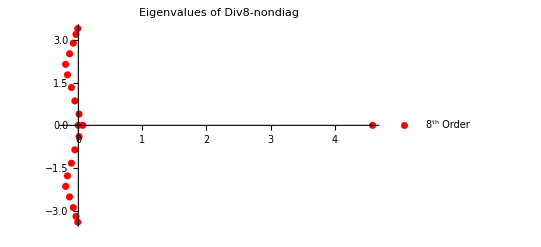

```mathematica
cplot8=ComplexListPlot[vals8,AspectRatio->1/GoldenRatio,PlotRange->All,PlotLabel->"Eigenvalues of Div8-nondiag",PlotStyle->Red,PlotLegends->{"8^th Order"}]
```

```mathematica
(lvals8=Sort[Eigenvalues[N[DDIV8*grad8]]])//MatrixForm
```

(-4.7596
-4.60283
-4.34028
-3.97556
-3.52372
-3.04047
-2.64107
-2.14147
-1.47263
-0.720657
0.
0.085
0.925767
1.77771
2.60982
3.3869
4.07387
4.64086
5.06849
5.3467
5.63561)

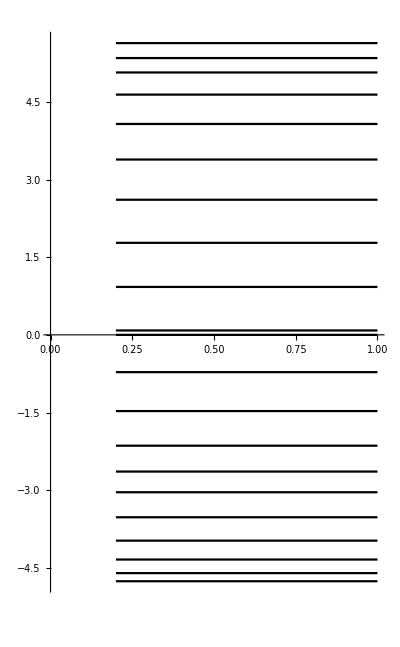

```mathematica
Plot[lvals8,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}]
```